```mathematica
Solve[{z==ω1/(1+ω2),ω==ω2/(1+ω2)},{ω1,ω2}]
```

{{ω1→-z/(ω-1),ω2→-ω/(ω-1)}}

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (-M2^2+M3^2 ω1))(M2^2+M1^2 ω1-M2^2 ω1-M3^2 ω1-M4^2 ω1+M3^2 ω1^2-√((-M2^2-M1^2 ω1+M2^2 ω1+M3^2 ω1+M4^2 ω1-M3^2 ω1^2)^2-4 (-M2^2+M3^2 ω1) (M4^2 ω1-M4^2 ω1^2)))
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (-M2^2+M3^2 ω1))(M2^2+M1^2 ω1-M2^2 ω1-M3^2 ω1-M4^2 ω1+M3^2 ω1^2+√((-M2^2-M1^2 ω1+M2^2 ω1+M3^2 ω1+M4^2 ω1-M3^2 ω1^2)^2-4 (-M2^2+M3^2 ω1) (M4^2 ω1-M4^2 ω1^2)))
```

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(M2-√(M2^2+4 M4^2 (z-1) z))/(2 M2)(*1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2-√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))*)
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
```

```mathematica
1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2-√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))/.{M1->M2,M3->M4}//Simplify
```

(M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z))/(2 M2^2)

```mathematica
ωfpm[z_][M1_,M2_,M3_,M4_]:=
(M2 √(M2^2+4 M4^2 z^2-4 M4^2 z)+M2^2)/(2 M2^2)
```

```mathematica
ωfp[0.5][141.05702953921949,141.05702953921949,140.32200110888644,140.32200110888644]
```

0.550977

```mathematica
ωfpm[0.5][141.05702953921949,141.05702953921949,140.32200110888644,140.32200110888644]
```

0.550977

```mathematica
Solve[M1^2/(1-z)+M2^2/z==M3^2/(1-ω)+M4^2/ω,ω]
```

{{ω→(M2^2-M2 √(M2^2+4 M4^2 z^2-4 M4^2 z))/(2 M2^2)},{ω→(M2 √(M2^2+4 M4^2 z^2-4 M4^2 z)+M2^2)/(2 M2^2)}}

```mathematica
(M2^2-M2 √(M2^2+4 M4^2 z^2-4 M4^2 z))/(2 M2^2)//Simplify
```

(M2-√(M2^2+4 M4^2 (z-1) z))/(2 M2)

```mathematica
1/(2 (-M1^2+M1^2 z-M2^2 z))(-M1^2+M1^2 z-M2^2 z-M3^2 z+M4^2 z+M3^2 z^2-M4^2 z^2-√(-4 (-M1^2+M1^2 z-M2^2 z) (-M3^2 z+M3^2 z^2)+(M1^2-M1^2 z+M2^2 z+M3^2 z-M4^2 z-M3^2 z^2+M4^2 z^2)^2))/.{M1->M2,M3->M4}
```

```mathematica
M1=M2;M3=M4;
```

```mathematica
ω2n[-z/(ωfp[z][M1,M2,M3,M4]-1)][M1,M2,M3,M4]//Simplify
```

(-M2^4-4 M2^2 M4^2 z^2+4 M2^2 M4^2 z+M2^2 √(M2^4+4 M2^2 M4^2 (z-1) z)-2 M4^2 z √(M2^4+4 M2^2 M4^2 (z-1) z)+4 M4^2 z^2 √((M2^8 (-M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z)+2 M4^2 z)^2)/((M2^2-√(M2^4+4 M2^2 M4^2 (z-1) z))^4))+2 M2^2 √((M2^8 (-M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z)+2 M4^2 z)^2)/((M2^2-√(M2^4+4 M2^2 M4^2 (z-1) z))^4))-4 M4^2 z √((M2^8 (-M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z)+2 M4^2 z)^2)/((M2^2-√(M2^4+4 M2^2 M4^2 (z-1) z))^4))-2 √(M2^4+4 M2^2 M4^2 (z-1) z) √((M2^8 (-M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z)+2 M4^2 z)^2)/((M2^2-√(M2^4+4 M2^2 M4^2 (z-1) z))^4)))/((√(M2^4+4 M2^2 M4^2 (z-1) z)-M2^2) (-M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z)+2 M4^2 z))

```mathematica
-(ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1)//Simplify
```

-(M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z))/(√(M2^4+4 M2^2 M4^2 (z-1) z)-M2^2)

```mathematica
%-%%//Simplify
```

(M2^4-M2^2 (√(M2^4+4 M2^2 M4^2 (z-1) z)+2 √2 √((M2^8 (M2^4-M2^2 (√(M2^4+4 M2^2 M4^2 (z-1) z)-2 M4^2 (z-2) z)+2 M4^2 z (√(M2^4+4 M2^2 M4^2 (z-1) z)+M4^2 z)))/(M2^2-√(M2^4+4 M2^2 M4^2 (z-1) z))^4)+2 M4^2 z)+2 √2 (√(M2^4+4 M2^2 M4^2 (z-1) z)-2 M4^2 (z-1) z) √((M2^8 (M2^4-M2^2 (√(M2^4+4 M2^2 M4^2 (z-1) z)-2 M4^2 (z-2) z)+2 M4^2 z (√(M2^4+4 M2^2 M4^2 (z-1) z)+M4^2 z)))/(M2^2-√(M2^4+4 M2^2 M4^2 (z-1) z))^4))/((√(M2^4+4 M2^2 M4^2 (z-1) z)-M2^2) (-M2^2+√(M2^4+4 M2^2 M4^2 (z-1) z)+2 M4^2 z))

```mathematica
Manipulate[Plot[%,{z,-8,8}],{M1,-8,8},{M2,-2,2},{M3,-2,2},{M4,-2,2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

```mathematica
%11-%7//Simplify
```

(-z M1^2+M1^2-M3^2 z^2+M4^2 z^2+M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))/(z M1^2-M1^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))-((2 z (M1^2 (z-1)-M2^2 z) M1^2)/(z M1^2-M1^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))+M2^2+√((8 z (M1^2 (z-1)-M2^2 z) (-2 z^2 M1^2+3 z M1^2-M1^2+2 M2^2 z^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z))) (-z M2^4-M1^2 M2^2+M3^2 z^2 M2^2+M4^2 z^2 M2^2+M1^2 z M2^2+M3^2 z M2^2-M4^2 z M2^2+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)) M2^2-2 M1^2 M3^2 z^2+2 M1^2 M3^2 z) M4^2)/(z M1^2-M1^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))^3+((2 z (M1^2 (z-1)-M2^2 z) M1^2)/(z M1^2-M1^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))+M2^2+(2 M3^2 z (M1^2 (z-1)-M2^2 z))/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))-(2 M2^2 z (M2^2 z-M1^2 (z-1)))/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))-(2 M4^2 z (M1^2 (z-1)-M2^2 z))/(z M1^2-M1^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))+(4 M3^2 z^2 (M1^2 (z-1)-M2^2 z)^2)/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))^2)^2)+(2 M3^2 z (M1^2 (z-1)-M2^2 z))/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))-(2 M2^2 z (M2^2 z-M1^2 (z-1)))/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))-(2 M4^2 z (M1^2 (z-1)-M2^2 z))/(z M1^2-M1^2-M3^2 z^2+M4^2 z^2-M2^2 z+M3^2 z-M4^2 z+√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))+(4 M3^2 z^2 (M1^2 (z-1)-M2^2 z)^2)/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))^2)/(2 (M2^2+(2 M3^2 z (M1^2 (z-1)-M2^2 z))/(-z M1^2+M1^2+M3^2 z^2-M4^2 z^2+M2^2 z-M3^2 z+M4^2 z-√(((z-1) M1^2-M2^2 z+(M3^2-M4^2) (z-1) z)^2-4 M3^2 (z-1) z (M1^2 (z-1)-M2^2 z)))))

```mathematica
Manipulate[Plot[%13,{z,-8,8}],{M1,-8,8},{M2,-2,2},{M3,-2,2},{M4,-2,2}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 4+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 3.3124+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
MVGva={{0.1,2.237724202176443*^-6},{0.2,0.000012127394775821504},{0.30000000000000004,0.00004929335224890318},{0.305,0.00005267291720760066},{0.31,0.000056270058447447553},{0.315,0.00006009852693722103},{0.32,0.0000641729661465122},{0.325,0.00006850897309085365},{0.32999999999999996,0.00007312316411899506},{0.33499999999999996,0.00007803324552181218},{0.33999999999999997,0.00008325808941897695},{0.345,0.000088817815726},{0.35,0.00009473387939429499},{0.355,0.00010102916536311084},{0.36,0.00010772808964013384},{0.365,0.0001148567090037121},{0.37,0.0001224428371373989},{0.375,0.00013051617832873091},{0.38,0.00013910844990317476},{0.385,0.00014825354617705163},{0.39,0.00015798768447766983},{0.395,0.0001683495842442704},{0.4,0.0001793806486206074},{0.40499999999999997,0.00019112516404394406},{0.41,0.0002036305221863709},{0.415,0.0002169474414126637},{0.42,0.00023113023074497772},{0.425,0.0002462370313867173},{0.43,0.0002623302407176244},{0.435,0.00027947657781123627},{0.44,0.000297747684932664},{0.445,0.000317220374257524},{0.45,0.000337977061362783},{0.45499999999999996,0.0003601062207224497},{0.45999999999999996,0.0003837027974099344},{0.46499999999999997,0.0004088688613677757},{0.47,0.00043571403889030463},{0.475,0.00046435619594612486},{0.48,0.0004949220883032361},{0.485,0.00052754809131952},{0.49,0.0005623809937400289},{0.495,0.0005995788549612057},{0.5,0.0006393119462246365},{0.505,0.0006817637696455883},{0.51,0.0007271321916605303},{0.515,0.0007756306288237666},{0.52,0.0008274894103884555},{0.525,0.0008829572148190475},{0.53,0.0009423026529467582},{0.535,0.0010058160301030807},{0.54,0.0010738112154637244},{0.545,0.0011466269179611134},{0.55,0.00122463307074127},{0.5549999999999999,0.0013082250993853026},{0.5599999999999999,0.0013978349129737933},{0.565,0.0014939297349463626},{0.57,0.0015970162575475913},{0.575,0.0017076443248910183},{0.5800000000000001,0.0018264107564426963},{0.5850000000000001,0.0019539638528849297},{0.5900000000000001,0.0020910081336940555},{0.5950000000000001,0.0022383096476234817},{0.6000000000000001,0.0023967016898725616},{0.605,0.0025670915326069734},{0.61,0.0027504670267593343},{0.615,0.002947904661128942},{0.62,0.0031605780264932033},{0.625,0.003389767371827943},{0.63,0.003636869874186696},{0.635,0.0039034112045856707},{0.64,0.0041910581908689},{0.645,0.004501632708415649},{0.65,0.004837127560107855},{0.655,0.00519972248448483},{0.66,0.005591804012914631},{0.665,0.0060159855832471725},{0.67,0.0064751301126313165},{0.675,0.006972376010353014},{0.6799999999999999,0.007511164017492703},{0.6849999999999999,0.008095267042130372},{0.69,0.008728824894989858},{0.695,0.009416379848069386},{0.7,0.010162916734750565},{0.7050000000000001,0.010973906719654848},{0.7100000000000001,0.011855354456500971},{0.7150000000000001,0.01281384956006338},{0.7200000000000001,0.013856622088675595},{0.7250000000000001,0.014991601643299561},{0.73,0.016227479918342315},{0.735,0.017573782215104448},{0.74,0.019040927043045323},{0.745,0.020640306931242625},{0.75,0.022384356216354137},{0.755,0.02428662023270287},{0.76,0.026361820462259187},{0.765,0.028625865181976778},{0.77,0.031096066576869346},{0.775,0.03379089630577429},{0.78,0.0367301375298102},{0.785,0.03993480978941608},{0.79,0.04342704238523265},{0.795,0.04722388055928203},{0.8,0.05136627550385603},{0.8049999999999999,0.05586036092678563},{0.8099999999999999,0.060734993339631504},{0.815,0.06601147111916285},{0.82,0.07170829879618847},{0.825,0.07783941210836551},{0.8300000000000001,0.08441196491807468},{0.8350000000000001,0.09142322382669202},{0.8400000000000001,0.09885727254121676},{0.8450000000000001,0.10667982248648535},{0.8500000000000001,0.11483283841059574},{0.855,0.12322740051974153},{0.86,0.13173555459351857},{0.865,0.1401808478483763},{0.87,0.14832919362079272},{0.875,0.15587808791595106},{0.8799999999999999,0.16245004837325772},{0.8849999999999999,0.1675868655344271},{0.8899999999999999,0.17071792727372995},{0.8949999999999999,0.17137565116426154},{0.9,0.16883786409153553},{0.903,0.16556612678631147},{0.906,0.16086026689004396},{0.909,0.15465280831900455},{0.912,0.14691770096464973},{0.915,0.1376822783269701},{0.918,0.12703974266877088},{0.921,0.11515944830262315},{0.924,0.10229354234007738},{0.927,0.08877698735500489},{0.93,0.07501844797463654},{0.933,0.06147936196361035},{0.936,0.04864037931840934},{0.9390000000000001,0.036950655516108585},{0.9420000000000001,0.026803301391365643},{0.9450000000000001,0.01843162220207339},{0.9480000000000001,0.011927646803161702},{0.9510000000000001,0.007205429450969701},{0.9540000000000001,0.0040298432476664325},{0.9570000000000001,0.002070371576507856},{0.96,0.000970966544772787},{0.963,0.0004142846739502707},{0.966,0.00016099355890057492},{0.969,0.00005734147534046561},{0.972,0.000018910611778476582},{0.975,5.831401212342225*^-6},{0.978,1.6864460997370767*^-6},{0.981,4.5293245645490496*^-7},{0.984,1.1040695174052267*^-7},{0.987,2.3632086614956624*^-8},{0.99,4.370696738913924*^-9},{0.993,6.152631691600617*^-10},{0.996,3.964240786860887*^-11},{0.999,9.939052424479043*^-14}};
```

```mathematica
MHGva={{0.1,0.000029928330981989932},{0.2,0.00007957136408202644},{0.30000000000000004,0.00019675944895894255},{0.303,0.00020224405817628085},{0.306,0.00020788884819287153},{0.309,0.00021369890749500868},{0.312,0.00021967949445783307},{0.315,0.00022583604980558927},{0.318,0.00023217420125367806},{0.321,0.00023869977215702773},{0.324,0.00024541878716523877},{0.327,0.00025233748119914774},{0.32999999999999996,0.0002594623068289365},{0.33299999999999996,0.0002667999447657729},{0.33599999999999997,0.0002743573100279773},{0.33899999999999997,0.0002821415623368797},{0.34199999999999997,0.00029016011599875365},{0.345,0.0002984206497540147},{0.348,0.0003069311171540827},{0.351,0.0003156997569906457},{0.354,0.00032473510698122806},{0.357,0.00033404583101738185},{0.36,0.00034364163682519934},{0.363,0.0003535314849713117},{0.366,0.00036372540415818616},{0.369,0.000374233599494622},{0.372,0.0003850666789748242},{0.375,0.0003962356011910189},{0.378,0.0004077517625426026},{0.381,0.0004196269748295507},{0.384,0.0004318734941399037},{0.387,0.00044450403853879875},{0.39,0.0004575318025552385},{0.393,0.00047097048440211144},{0.396,0.000484834301717041},{0.399,0.0004991380185053617},{0.402,0.0005138969616216382},{0.405,0.0005291270495979483},{0.40800000000000003,0.0005448448166290884},{0.41100000000000003,0.0005610674385464914},{0.41400000000000003,0.0005778127609351275},{0.41700000000000004,0.0005950993285696401},{0.42,0.0006129464135989154},{0.423,0.0006313740496494307},{0.426,0.0006504030644044319},{0.429,0.0006700551139290175},{0.432,0.0006903527194309278},{0.435,0.0007113193057654766},{0.438,0.0007329792566456384},{0.441,0.0007553578853315439},{0.444,0.0007784816178485406},{0.447,0.0008023779032467334},{0.44999999999999996,0.0008270753298062091},{0.45299999999999996,0.0008526036623699712},{0.45599999999999996,0.0008789938939011608},{0.45899999999999996,0.0009062783126624075},{0.46199999999999997,0.0009344905379996947},{0.46499999999999997,0.0009636656099868289},{0.46799999999999997,0.0009938400442133233},{0.471,0.0010250518927649099},{0.474,0.0010573408258932435},{0.477,0.00109074820486387},{0.48,0.0011253171645009457},{0.483,0.0011610926935736237},{0.486,0.001198121727224012},{0.489,0.001236453239560956},{0.492,0.0012761383397075768},{0.495,0.0013172303788236966},{0.498,0.0013597850153740094},{0.501,0.0014038605417592553},{0.504,0.0014495175803552081},{0.507,0.0014968196407757343},{0.51,0.0015458330317010575},{0.513,0.001596627061579958},{0.516,0.0016492741715609493},{0.519,0.0017038501101749753},{0.522,0.0017604340904112067},{0.525,0.0018191089549325044},{0.528,0.001879961381379783},{0.531,0.0019430820962020865},{0.534,0.002008566030333741},{0.537,0.002076512580222755},{0.54,0.0021470258305121177},{0.543,0.002220214792687035},{0.546,0.0022961936750219335},{0.549,0.0023750821486830335},{0.552,0.0024570069060713476},{0.555,0.002542096939965327},{0.558,0.0026304913996600954},{0.561,0.0027223349160098585},{0.5640000000000001,0.0028177792290048857},{0.5670000000000001,0.002916983578353345},{0.5700000000000001,0.003020115101671581},{0.5730000000000001,0.003127349295594806},{0.5760000000000001,0.0032388704510866646},{0.5790000000000001,0.0033548721628192508},{0.5820000000000001,0.003475556525252001},{0.5850000000000001,0.003601139978110374},{0.5880000000000001,0.0037318461833851474},{0.5910000000000001,0.0038679108247890617},{0.5940000000000001,0.004009583172123254},{0.5970000000000001,0.00415712460488739},{0.6,0.004310810379273679},{0.603,0.004470930307930174},{0.606,0.004637789564802282},{0.609,0.0048117095920753705},{0.612,0.004993029071038656},{0.615,0.0051821049488582445},{0.618,0.005379313523999284},{0.621,0.005585051636569982},{0.624,0.005799737905019236},{0.627,0.006023814021270142},{0.63,0.006257746198467133},{0.633,0.00650202668477041},{0.636,0.006757175651302749},{0.639,0.007023741431603243},{0.642,0.007302305360300475},{0.645,0.007593480768410367},{0.648,0.007897916459580075},{0.651,0.008216298878006253},{0.654,0.00854935428576407},{0.657,0.008897851408666928},{0.6599999999999999,0.009262604315270042},{0.6629999999999999,0.009644475136187228},{0.6659999999999999,0.010044377473964},{0.6689999999999999,0.010463279406218376},{0.6719999999999999,0.010902207548239506},{0.6749999999999999,0.01136225059653457},{0.6779999999999999,0.01184456380635686},{0.6809999999999999,0.012350372985941514},{0.6839999999999999,0.012880979890086741},{0.6869999999999999,0.013437766597971738},{0.69,0.01402220171675058},{0.693,0.014635845984994785},{0.696,0.015280358518072627},{0.699,0.01595750415442831},{0.702,0.016669159639340177},{0.705,0.017417322842723234},{0.708,0.018204120470288097},{0.711,0.019031817293360908},{0.714,0.019902825557165462},{0.717,0.020819716377825013},{0.72,0.021785230096942814},{0.723,0.022802288524477493},{0.726,0.02387400928777943},{0.729,0.025003717171082806},{0.732,0.026194961797520098},{0.735,0.027451532497341023},{0.738,0.028777475772357015},{0.741,0.030177114245139813},{0.744,0.03165506639172674},{0.747,0.03321626839282096},{0.75,0.034865996686142736},{0.753,0.036609892967064524},{0.756,0.038453990750339825},{0.759,0.04040474297132655},{0.762,0.04246905015948264},{0.765,0.044654305534479424},{0.768,0.04696840596453339},{0.771,0.04941980701945242},{0.774,0.05201755472115768},{0.777,0.05477133701022553},{0.78,0.057691504225161463},{0.783,0.06078913912809857},{0.786,0.06407608591353188},{0.789,0.06756501552483167},{0.792,0.07126946571139925},{0.795,0.07520389896225496},{0.798,0.07938375457670406},{0.801,0.0838255029532548},{0.804,0.08854670266604235},{0.807,0.0935660461230468},{0.81,0.09890341119864027},{0.8130000000000001,0.1045799073043854},{0.8160000000000001,0.11061791383372582},{0.8190000000000001,0.11704109454081457},{0.8220000000000001,0.1238744333165707},{0.8250000000000001,0.13114420742305746},{0.8280000000000001,0.13887797314606073},{0.8310000000000001,0.1471045029508398},{0.8340000000000001,0.15585366052584043},{0.8370000000000001,0.16515640491716974},{0.8400000000000001,0.17504428835777078},{0.8430000000000001,0.18554947183745185},{0.8460000000000001,0.19670420305980346},{0.8490000000000001,0.20854035923565623},{0.8520000000000001,0.2210888129784639},{0.8550000000000001,0.23437863944923204},{0.8580000000000001,0.24843610297309818},{0.8610000000000001,0.2632833925433185},{0.8640000000000001,0.2789370873818143},{0.867,0.2954063012763825},{0.87,0.31269008323460884},{0.873,0.3307749111979049},{0.876,0.34963139301950424},{0.879,0.36920978875264937},{0.882,0.3894356543498342},{0.885,0.41020415079008554},{0.888,0.43137372507332167},{0.891,0.45275902523992995},{0.8939999999999999,0.4741225171384246},{0.8969999999999999,0.4951668015836405},{0.8999999999999999,0.5155247614764431},{0.9029999999999999,0.5347516087690671},{0.9059999999999999,0.5523172551248889},{0.9089999999999999,0.5676010374815424},{0.9119999999999999,0.5798905722392054},{0.9149999999999999,0.5883875856597016},{0.9179999999999999,0.5922213963897178},{0.921,0.5904788644312307},{0.924,0.5822488648857334},{0.927,0.5666902334602891},{0.93,0.5431243910532627},{0.933,0.5111536974926862},{0.936,0.4708015776935634},{0.9390000000000001,0.422660125589858},{0.9420000000000001,0.36802028782851626},{0.9450000000000001,0.30894883211885843},{0.948,0.24824377617049653},{0.951,0.1892408811727943},{0.954,0.13541081167559424},{0.957,0.08978560911084607},{0.96,0.05433146149399279},{0.963,0.02948094805509128},{0.966,0.014069356302576792},{0.969,0.005792181062856443},{0.972,0.0020246018724804377},{0.9750000000000001,0.0005965729928615969},{0.9780000000000001,0.00014912451787198105},{0.9810000000000001,0.00003216398752320886},{0.9840000000000001,6.046373011857746*^-6},{0.9870000000000001,9.65031424440136*^-7},{0.9900000000000001,1.1885874607370028*^-7},{0.9930000000000001,9.579865865404331*^-9},{0.9960000000000001,4.186829536391511*^-10},{0.9990000000000001,6.903361188810339*^-13}};
```

```mathematica
Sω1[ω1_]=Interpolation[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.00001,1,0.01}]][ω1];
```

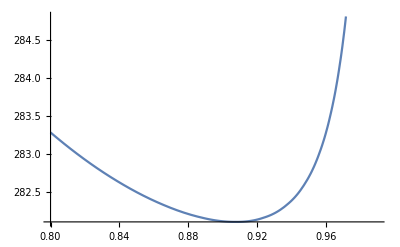

```mathematica
Plot[Sω1[ω1],{ω1,0.8,0.99}]
```

```mathematica
Sω1[0.95]
```

282.699

```mathematica
Interpolation[MHGva]
```

InterpolatingFunction[{{0.1, 0.999}}, <>]

```mathematica
Table[{Sω1[x],Interpolation[MVGva][x]+Interpolation[MHGva][x]},{x,0.9,0.999,0.001}]
```

(282.122 | 0.684363
282.12 | 0.689986
282.118 | 0.695312
282.117 | 0.700318
282.115 | 0.704982
282.115 | 0.709277
282.114 | 0.713178
282.114 | 0.71666
282.114 | 0.719694
282.114 | 0.722254
282.114 | 0.724312
282.115 | 0.72584
282.116 | 0.726808
282.118 | 0.727189
282.12 | 0.726952
282.123 | 0.72607
282.126 | 0.724511
282.13 | 0.722251
282.134 | 0.719261
282.138 | 0.71551
282.144 | 0.710977
282.149 | 0.705638
282.156 | 0.699462
282.163 | 0.692436
282.17 | 0.684542
282.178 | 0.675751
282.186 | 0.666062
282.195 | 0.655467
282.204 | 0.643939
282.214 | 0.631497
282.226 | 0.618143
282.238 | 0.603858
282.251 | 0.588681
282.265 | 0.572633
282.28 | 0.555705
282.296 | 0.537962
282.314 | 0.519442
282.332 | 0.500153
282.351 | 0.480188
282.371 | 0.459611
282.392 | 0.438452
282.414 | 0.416828
282.438 | 0.394824
282.464 | 0.372495
282.492 | 0.349978
282.522 | 0.32738
282.553 | 0.304791
282.587 | 0.282348
282.623 | 0.260171
282.66 | 0.238383
282.699 | 0.217101
282.741 | 0.196446
282.786 | 0.176564
282.834 | 0.157529
282.886 | 0.139441
282.942 | 0.122453
283.002 | 0.106571
283.064 | 0.091856
283.13 | 0.0784401
283.202 | 0.0662542
283.279 | 0.0553024
283.363 | 0.0456642
283.453 | 0.0372125
283.55 | 0.0298952
283.653 | 0.0237125
283.764 | 0.0185212
283.886 | 0.0142303
284.018 | 0.0107612
284.163 | 0.00800103
284.317 | 0.00584952
284.486 | 0.00418167
284.672 | 0.00294028
284.877 | 0.00204351
285.1 | 0.0013683
285.346 | 0.000904907
285.619 | 0.000602404
285.922 | 0.000374328
286.258 | 0.000231897
286.635 | 0.000150811
287.058 | 0.0000863027
287.534 | 0.0000498882
288.075 | 0.0000326169
288.691 | 0.0000170828
289.398 | 9.13243×10^-6
290.213 | 6.15678×10^-6
291.162 | 2.90727×10^-6
292.276 | 1.39431×10^-6
293.595 | 9.88664×10^-7
295.174 | 3.97432×10^-7
297.089 | 1.52785×10^-7
299.445 | 1.23229×10^-7
302.395 | 3.40058×10^-8
306.162 | 4.3413×10^-9
311.1 | 1.01951×10^-8
317.779 | 1.14903×10^-10
327.2 | -1.96998×10^-9
341.279 | 4.58325×10^-10
364.195 | 3.91766×10^-9
407.272 | 4.92587×10^-9
517.514 | 7.89727×10^-13)

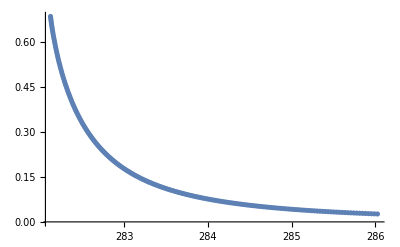

```mathematica
ListPlot[Table[{Sω1[x],Interpolation[MVGva][x]+Interpolation[MHGva][x]},{x,0.7,0.9,0.001}]]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
S[z_][M1_,M2_]:=M1^2+M2^2+M1^2(1/z-1)^-1+M2^2(1/z-1);
```

```mathematica
Block[{mQ=80,mq=60},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.